```mathematica
<<MaTeX`
restyleWithSort[p_,op:OptionsPattern[ListLinePlot]]:=ListLinePlot[Cases[Normal@p,Line[x__]:>x,∞]~SortBy~Extract[{1,2}],op,Options[p]]
```

## Analytic Example

## M = 4, α = 0

```mathematica
M=4;
α=0;
ub[t_,n_]:=1/2(-t+√((2M-t)^2+(n π)^2))
```

```mathematica
G1=Plot[{ub[t,1],ub[t,2],ub[t,3],ub[t,4],ub[t,5]},{t,0,2M},PlotRange->{-3,M},PlotStyle->Dashed];
G2=restyleWithSort/@ContourPlot[{Tan[√((M+λ+α t)(λ-(M-t)))]==√((M^2-λ^2)/((λ-(M-t))(λ+M+α t))),Tan[√((M+λ+α t)(λ-(M-t)))]==-1(√((M^2-λ^2)/((λ-(M-t))(λ+M+α t))))^-1},{t,0,2M},{λ,-3,M},PerformanceGoal->"Quality",PlotPoints->100,MaxRecursion->3];
```

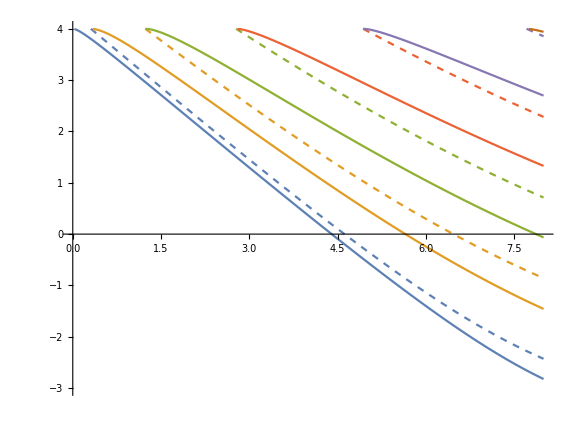

```mathematica
Show[{G1,G2},Frame->False,Axes->True,AxesOrigin->{0,0},AspectRatio->3/4,AxesLabel->{MaTeX["t",FontSize->15],MaTeX["\\lambda",FontSize->15]},ImageSize->Large]
```

## M = 4, α = 1

```mathematica
M=4;
α=1;
ub[t_,n_]:=-t+1/2 √(4 M^2+(n π)^2)
```

```mathematica
G1=Plot[{ub[t,1],ub[t,2],ub[t,3],ub[t,4],ub[t,5],ub[t,6],ub[t,7]},{t,0,2M},PlotRange->{-M,M},PlotStyle->{{ColorData[97,1],Dashed},{ColorData[97,8],Dashed},{ColorData[97,2],Dashed},{ColorData[97,3],Dashed},{ColorData[97,9],Dashed},{ColorData[97,4],Dashed},{ColorData[97,5],Dashed}}];
G2=restyleWithSort/@ContourPlot[{Tan[√((M+λ+α t)(λ-(M-t)))]==√((M^2-λ^2)/((λ-(M-t))(λ+M+α t))),Tan[√((M+λ+α t)(λ-(M-t)))]==-1(√((M^2-λ^2)/((λ-(M-t))(λ+M+α t))))^-1},{t,0,2M},{λ,-M,M},PerformanceGoal->"Quality",PlotPoints->100,MaxRecursion->3];
```

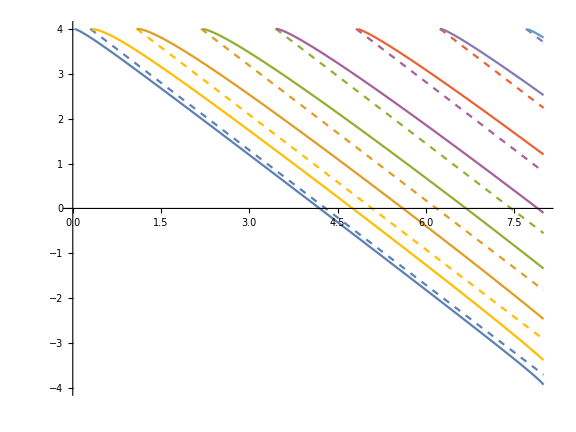

```mathematica
Show[{G1,G2},Frame->False,Axes->True,AxesOrigin->{0,0},AspectRatio->3/4,AxesLabel->{MaTeX["t",FontSize->15],MaTeX["\\lambda",FontSize->15]},ImageSize->Large]
```

## M = 4, α = -1

```mathematica
M=4;
α=-1;
ub[t_,n_]:=1/2(√(4(M-t)^2+(n π)^2))
```

```mathematica
G1=Plot[{ub[t,1],ub[t,2]},{t,0,M},PlotRange->{1,M},PlotStyle->Dashed];
G2=restyleWithSort/@ContourPlot[{Tan[√((M+λ+α t)(λ-(M-t)))]==√((M^2-λ^2)/((λ-(M-t))(λ+M+α t))),Tan[√((M+λ+α t)(λ-(M-t)))]==-1(√((M^2-λ^2)/((λ-(M-t))(λ+M+α t))))^-1},{t,0,M},{λ,1,M},PerformanceGoal->"Quality",PlotPoints->100,MaxRecursion->3];
```

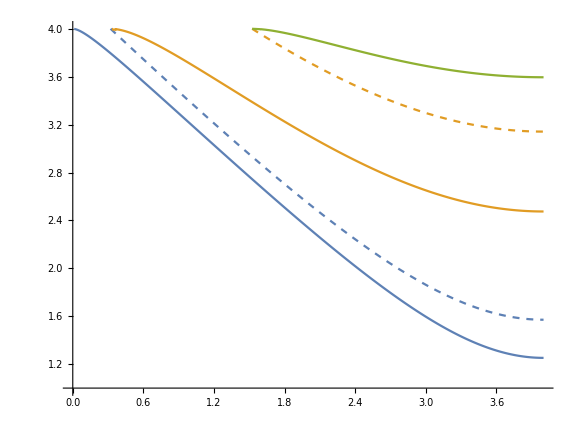

```mathematica
Show[{G1,G2},Frame->False,Axes->True,AxesOrigin->{0,1},AspectRatio->3/4,AxesLabel->{MaTeX["t",FontSize->15],MaTeX["\\lambda",FontSize->15]},ImageSize->Large]
```

## Numerical Example (Data from Python code)

```mathematica
SetDirectory[NotebookDirectory[]];
Data=Import["(t,lambda).csv","CSV","HeaderLines"->1];
```

```mathematica
G2=ListPlot[Data,PlotStyle->Blue];
```

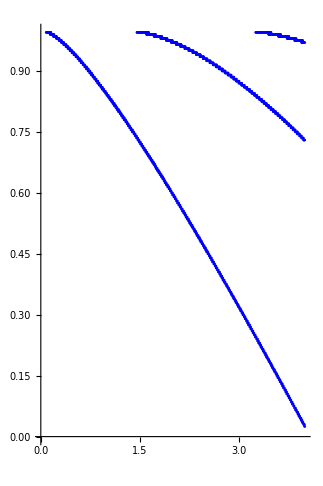

```mathematica
Show[G2,Frame->False,Axes->True,AxesOrigin->{0,0},AspectRatio->217/144,AxesLabel->{MaTeX["t",FontSize->15],MaTeX["\\lambda",FontSize->15]}]
```